# Packages

## Basic Exercises

### Question Subsection

Take the exercise notebook from Functions Part I and convert it into a package. Make sure you add usage messages. 
As a bonus, you can think of adding options to your functions.

#### Solution

The package file we used is attached with the name FunctionExercises.m.

```mathematica
PrependTo[$Path, NotebookDirectory[]];
```

```mathematica
<<FunctionExercises`
```

```mathematica
?mySum
```

mySum[a,b] adds the two numbers a and b.
mySum[a] adds the sequence of numbers a together.

```mathematica
mySum[a_,b_]:=a+b
```

```mathematica
mySum[3,4]
```

7

```mathematica
mySum[1,2,3]
```

6

```mathematica
?separate
```

separate[a] takes a list of numbers and highlights them according to their sign.

```mathematica
separate[2]
```

2

```mathematica
separate[-2]
```

-2

```mathematica
separate[-2.2]
```

-2.2

```mathematica
mylist={-2,3.4,53,-3.33,4.4,23,82,34.5,-2.2,-9};
```

```mathematica
separate[mylist]
```

{-2,3.4,53,-3.33,4.4,23,82,34.5,-2.2,-9}

```mathematica
?trigPlot
```

trigPlot[fun,num] plots one of the functions fun (either Sin or Cos) and plots them with frequencies up to num in increments of 1.
trigPlot[fun] uses 3 as the default for num.

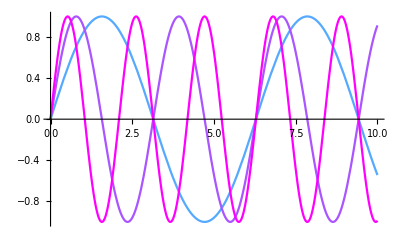

```mathematica
trigPlot[Sin]
```

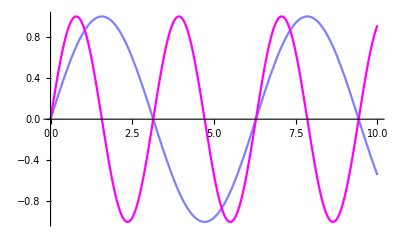

```mathematica
trigPlot[Sin,2]
```

```mathematica
?report
```

report[person] generates a report about a given person from our internal database.

```mathematica
report["John"]
```

name:John

Age:23

State:IL

Gender:M

```mathematica
report["Judy"]
```

name:Judy

Age:43

State:PA

Gender:F

```mathematica
?findroots
```

findroots[l] takes a list l of numbers which represent coefficients of a quadratic equation, and returns the roots.

```mathematica
findroots[3]
```

Input must be a list of real valued numbers

```mathematica
findroots[{3,1}]
```

Input must be a list of real valued numbers

```mathematica
findroots[{2,3,NotANumber}]
```

Input must be a list of real valued numbers

```mathematica
findroots[{1,2,3}]
```

{-1.+1.4 ⅈ,-1.-1.4 ⅈ}